# First Order Transition Algorithm Given an effective potential, one sets the sensitivity of the algorithm in the While loop. One can first choose an estimate of the temperature where first order phase transition will most likely occur and allow the algorithm to find the more accurate value. Equally, one can also set the temperature as zero and let the algorithm compute the critical temperature. (N.B The disadvantage of not setting an estimation prior to the algorithm is at the cost of longer computation time.)

## Case 1: Lagrangian de Kolb & Turner

Set::write: Tag Real in true:Blank[103.493] is Protected.

103.493

103.493

90

91

1

246

3/2

V_HTE =

-4050 ϕ^2+(91 ϕ^3)/3+ϕ^4/4+(-2.48327×10^8+8809.21 (-8100+182 ϕ+3 ϕ^2)-54.1886 (-8100+182 ϕ+3 ϕ^2)^(3/2))/(2 π^2)+((-8100+182 ϕ+3 ϕ^2)^2 (-3/2+Log[(-8100+182 ϕ+3 ϕ^2)/60516]))/(64 π^2)

Evaluate at ϕ =0

-1.656×10^7

0

75

0.03

Minimum value:

-0.0098203

10

minval:

-0.0098203

Changed temperature

103.493

New min:

-0.0098203

ϕ at V_HTE=0:

{}

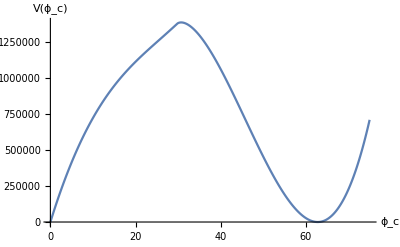

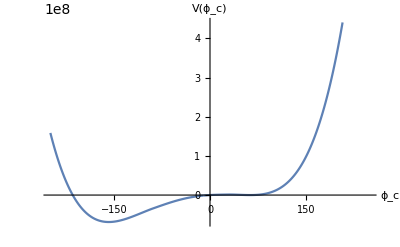

```mathematica
true_T = 103.4925952 (* this is the value of T one produced by inspection, producing Subscript[V, HTE]= -0.009*)
T = 103.4925952
m = 90
μ = 91
λ = 1
Q=246

c = 3/2
Subscript[V, HTE][ϕ_]:=-1/2*m^2*ϕ^2+ 1/3*μ*ϕ^3+1/4*λ*ϕ^4+ ((Sqrt[-m^2+ 2*μ*ϕ+3*λ*ϕ^2])^4)/(64*Pi^2)*(Log[((Sqrt[-m^2+ 2*μ*ϕ+3*λ*ϕ^2])^2)/Q^2]-c) +1/(2*Pi^2)*(-Pi^4/45*T^4+Pi^2/12*T^2*(Sqrt[-m^2+ 2*μ*ϕ+3*λ*ϕ^2])^2-Pi/6 T*(Sqrt[-m^2+ 2*μ*ϕ+3*λ*ϕ^2])^3)
"V_HTE = "
Subscript[V, HTE][ϕ]
"Evaluate at ϕ =0"
d = Evaluate[Re[Subscript[V, HTE][0]]] (* d is a constant that shifts the graph like a y-intercept*)

min = 0
max = 75
step = 0.03

(*minVal = FindMinimum[{Re[Subscript[V, HTE][ϕ]],150<ϕ<250},{ϕ,150}]*)

(*data = Table[Re[-1/2*m^2*ϕ^2+ 1/3*μ*ϕ^3+1/4*λ*ϕ^4+ ((Sqrt[-m^2+ 2*μ*ϕ+3*λ*ϕ^2])^4)/(64*Pi^2)*(Log[((Sqrt[-m^2+ 2*μ*ϕ+3*λ*ϕ^2])^2)/Q^2]-3/2) +1/(2*Pi^2)*(-Pi^4/45*T^4+Pi^2/12*T^2*(Sqrt[-m^2+ 2*μ*ϕ+3*λ*ϕ^2])^2-Pi/6 T*(Sqrt[-m^2+ 2*μ*ϕ+3*λ*ϕ^2])^3)-d
],{ϕ,min+1,max,step}];*)

"Minimum value:"
minval = Min[Table[Re[Subscript[V, HTE][ϕ]]-Re[Subscript[V, HTE][0]],{ϕ,min+1,max,step}]]

dT= 10

"minval:"
minval

(*"Loop begins"
"If minval <0 : {T,minval}; If minval >0 : {dT,T,minval}"
(*only subtract by dT if minval>0 since at low temperatures, the minimum is always below negative*)

sensitivity = 0.0001; (*the criteria in which the While loop will cease*)

While[Abs[minval] > sensitivity,If[minval>0,Print[{dT = dT/2, T = 1.*(T-dT), minval = Min[Table[Re[Subscript[V, HTE][ϕ]]-Re[Subscript[V, HTE][0]],{ϕ,min+1,max,step}]]}],If[minval <0, Print[{T = 1.*(T+dT), minval = Min[ Table[Re[Subscript[V, HTE][ϕ]]-Re[Subscript[V, HTE][0]],{ϕ,min+1,max,step}]]}]]]]
"Loop completed"*)

"Changed temperature"
T*1.

"New min:"
minval*1.

"ϕ at V_HTE=0:"
data = Table[Re[Subscript[V, HTE][ϕ]-Subscript[V, HTE][0]],{ϕ,0,max,step}];
 Position[data,minval]
data1=Table[Re[Subscript[V, HTE][ϕ]-Subscript[V, HTE][0]],{ϕ,-(2*max+100),2*max+100,step}];

c=.
ListPlot[data,Joined->True,AxesLabel->{Subscript[ϕ,c],V[Subscript[ϕ,c]]},DataRange->{0,max}](*9166=(max-(-max))/0.03*1/2*)(*AxesOrigin->{9166,0}*)
ListPlot[data1,Joined->True,AxesLabel->{Subscript[ϕ,c],V[Subscript[ϕ,c]]},DataRange->{-(2*max+100),2*max+100}]

(*If[min>0,Subscript[V, HTE][ϕ,T-dT],If[min <0, Subscript[V, HTE][ϕ,T+dT/2],"false"]];*)

(*Manipulate[ListPlot[Table[Re[-1/2*m^2*ϕ^2+ 1/3*μ*ϕ^3+1/4*λ*ϕ^4+ ((Sqrt[-m^2+ 2*μ*ϕ+3*λ*ϕ^2])^4)/(64*Pi^2)*(Log[((Sqrt[-m^2+ 2*μ*ϕ+3*λ*ϕ^2])^2)/Q^2]-3/2) +1/(2*Pi^2)*(-Pi^4/45*T^4+Pi^2/12*T^2*(Sqrt[-m^2+ 2*μ*ϕ+3*λ*ϕ^2])^2-Pi/6 T*(Sqrt[-m^2+ 2*μ*ϕ+3*λ*ϕ^2])^3)-d
],{ϕ,min,max,step}]],{T , 90,105,0.2},{μ,90,100,0.2},{m,90,100,0.2},{λ,0,2,0.1}]*)
```

```mathematica
λϕψ(OverBar[ψ])
```

λϕψ ψ̄